```mathematica
(*check*)
correl=Function[{x,y,z,L,ttilde},result=0;For[nx=-L,nx<L,nx=nx+1,For[ny=-L,ny<L,ny=ny+1,For[nz=-L,nz<L,nz=nz+1,
kx=2.0 Pi nx/L;ky=2.0 Pi ny/L;kz=2.0 Pi nz/L;
rho=4 (Cos[kx/2]Cos[ky/2]+Cos[kx/2]Cos[kz/2]+Cos[ky/2]Cos[kz/2]);
result=result+0.5Cos[kx x+ky y+kz z]0.5 ttilde rho/(1-ttilde rho)^(1/2); 
]]];
result=0.5 result/L^3
];
```

```mathematica
correl[0,1,1,2,0.01]
```

0.000220236

```mathematica
correl[1.5,0.5,1,2,0.01]
```

0.000220236

```mathematica
correl[1/2,-1/2,0,1,0.01]
```

0.0417859

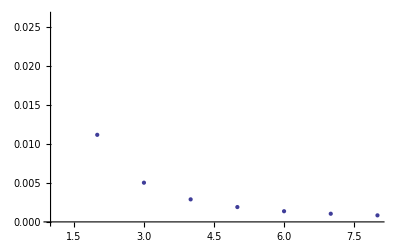

```mathematica
d1=Table[{n,correl[n,0,0,50,0.08333]},{n,1,8}];
ListPlot[d1]
```

```mathematica
d1
```

{{1,0.0329372},{2,0.0103275},{3,0.00486063},{4,0.00283796},{5,0.00188279},{6,0.00135941},{7,0.00104268},{8,0.000836964}}

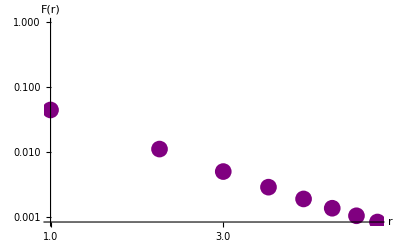

```mathematica
(*log-log plot, small distance. very close to condensation*)
ListLogLogPlot[d1,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Purple,PointSize[0.03]},AxesLabel->{Style["r",Italic,Large,"Times"],Style["F(r)",Italic,Large,"Times"]}]
```

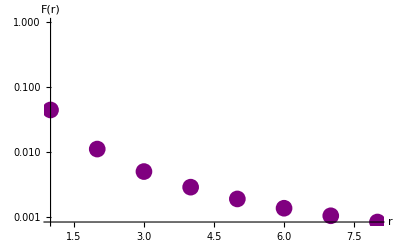

```mathematica
(*semi-log plot, small distance. very close to condensation*)
ListLogPlot[d1,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Purple,PointSize[0.03]},AxesLabel->{Style["r",Italic,Large,"Times"],Style["F(r)",Italic,Large,"Times"]}]
```

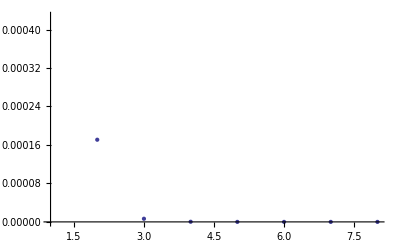

```mathematica
d2=Table[{n,correl[n,0,0,50,0.05]},{n,1,8}];
ListPlot[d2]
```

```mathematica
d2
```

{{1,0.00711446},{2,0.000170896},{3,6.55549×10^-6},{4,3.02668×10^-7},{5,1.54518×10^-8},{6,8.40304×10^-10},{7,4.77255×10^-11},{8,2.79782×10^-12}}

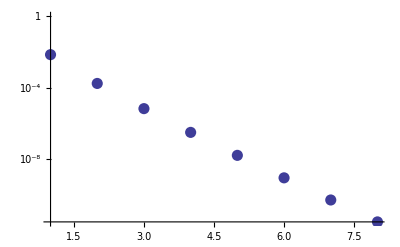

```mathematica
ListLogPlot[d2,BaseStyle->{FontSize->20,FontFamily->"Times"},PlotStyle->{PointSize[0.02]}]
```

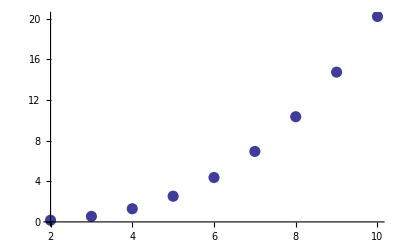

```mathematica
ff1=Table[{l,4 correl[1/2,1/2,0,l,0.005] l^3},{l,2,10}];
ListPlot[ff1,PlotStyle->{PointSize[0.02]}]
```

```mathematica
ff1
```

{{2,0.673051},{3,2.26336},{4,5.36492},{5,10.4784},{6,18.1066},{7,28.7526},{8,42.9194},{9,61.1098},{10,83.8269}}

```mathematica
correl[1/2,1/2,0,10,0.02]
```

0.0209567

```mathematica
6!
```

720

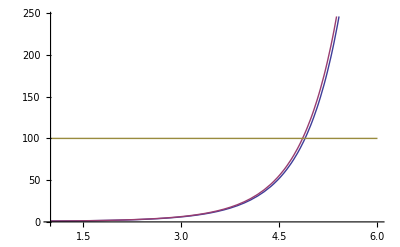

```mathematica
(*Compare several approximaitons*)
Plot[{m!,m^(1/2)E(m/E)^m,100},{m,1,6}]
```

```mathematica
l=0.025;
Plot[{m!-(l E+(2-l)(2Pi)^(1/2))/2( m)^(1/2)(m/E)^m},{m,1,100}]
```

-Graphics-

```mathematica
N[E-(2Pi)^(1/2)]
```

0.211654

```mathematica
N[E]
```

2.71828

```mathematica
N[(2Pi)^(1/2)]
```

2.50663